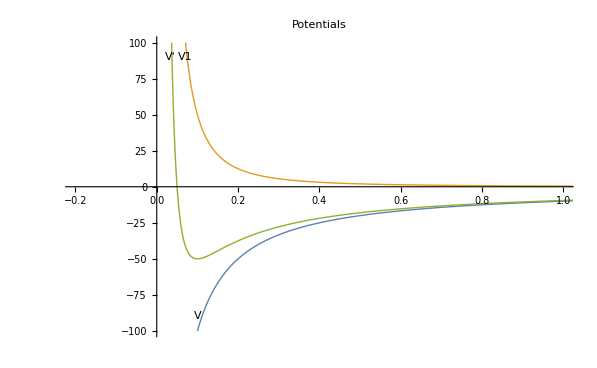

```mathematica
Plot[{-10/x,1/(2 x^2),-10/x+1/(2 x^2)},{x, 0,2}, PlotRange->{{-0.2,1},{-100, 100}},PlotStyle->Thick, PlotLabels->Placed[{"V","V1","V'"}, Left], PlotLabel->"Potentials"]
```

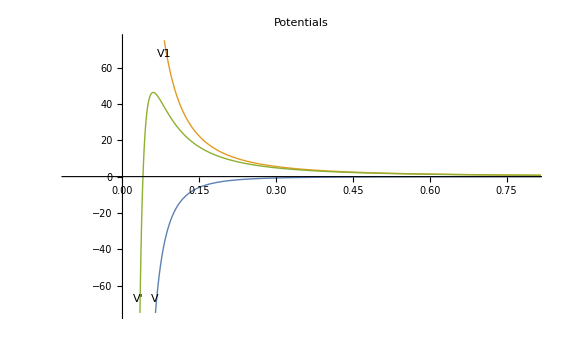

```mathematica
Plot[{-0.02/x^3,1/(2 x^2),-0.02/x^3+1/(2 x^2)},{x, 0,2}, PlotRange->{{-0.1,0.8},{-75, 75}},PlotStyle->Thick, PlotLabels->Placed[{"V","V1","V'"}, Left], PlotLabel->"Potentials"]
```

```mathematica
Manipulate[Plot[{-a/x^3,l^2/(2m x^2),-a/x^3+l^2/(2 m x^2)},{x, 0,2}, PlotRange->{{-0.1,0.8},{-75, 75}},PlotStyle->Thick, PlotLabels->Placed[{"V","V1","V'"}, Left], PlotLabel->"Potentials"],{a,0.01,0.1},{l,0.1,2},{m, 1, 2}]
```

```mathematica
Integrate[Sin[n π x/L]^2,{x,0, L}]
```

1/4 L (2-Sin[2 n π]/(n π))

```mathematica
Integrate[Sin[n π x/L]^2,x]
```

x/2-(L Sin[(2 n π x)/L])/(4 n π)

```mathematica
TeXForm[Integrate[2/L(x) Sin[(n π x)/L]^2,x]]
```

\frac{2 \left(-\frac{L^2 \cos
   \left(\frac{2 \pi  n x}{L}\right)}{8
   \pi ^2 n^2}-\frac{L x \sin
   \left(\frac{2 \pi  n x}{L}\right)}{4
   \pi  n}+\frac{x^2}{4}\right)}{L}

```mathematica
TeXForm[Integrate[2/L(x) Sin[(n π x)/L]^2,{x, 0, L}]]
```

-\frac{L \left(-2 \pi ^2 n^2+2 \pi  n
   \sin (2 \pi  n)+\cos (2 \pi 
   n)-1\right)}{4 \pi ^2 n^2}

```mathematica
TeXForm[Integrate[2/L(x^2) Sin[(n π x)/L]^2,x]]
```

\frac{2 \left(-\frac{L^2 x \cos
   \left(\frac{2 \pi  n x}{L}\right)}{4
   \pi ^2 n^2}-\frac{L \left(2 \pi ^2
   n^2 x^2-L^2\right) \sin
   \left(\frac{2 \pi  n x}{L}\right)}{8
   \pi ^3 n^3}+\frac{x^3}{6}\right)}{L}

```mathematica
TeXForm[Integrate[2/L(x^2) Sin[(n π x)/L]^2,{x, 0, L}]]
```

\frac{L^2 \left(4 \pi ^3 n^3+\left(3-6
   \pi ^2 n^2\right) \sin (2 \pi  n)-6
   \pi  n \cos (2 \pi  n)\right)}{12
   \pi ^3 n^3}

```mathematica
TeXForm[Integrate[ Sin[(n π x)/L]^2,x]]
```

\frac{x}{2}-\frac{L \sin \left(\frac{2
   \pi  n x}{L}\right)}{4 \pi  n}